```mathematica
Clear[ϵn,kx,ky,t];

ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);t=0.3;
```

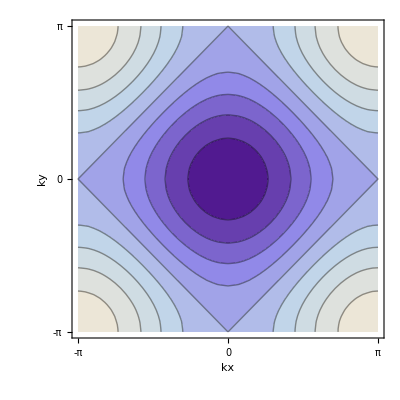

```mathematica
Image1=ContourPlot[ϵn[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1.png",Image1]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1.png

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky]
```

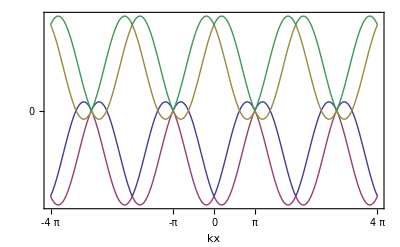

```mathematica
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2];t=0.3;

α=0.4;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
Image2=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-2,0,2},None},{{-Pi,-4 Pi,0,Pi,4 Pi},None}}]
```

```mathematica
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1+alpha.png",Image2]
```

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1+alpha.png

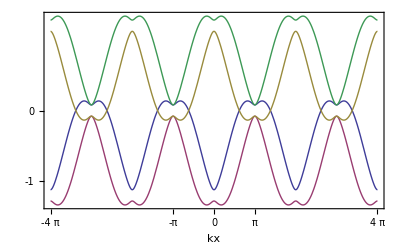

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1+alpha+mx.png

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky]
ϵn[kx_,ky_]:=-2*t*(Cos[kx]+Cos[ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];t=0.3;
α=0.4;mz=0.2;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
Image3=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-2,-1,0},None},{{-Pi,-4 Pi,0,Pi,4 Pi},None}}]
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1+alpha+mx.png",Image3]
```

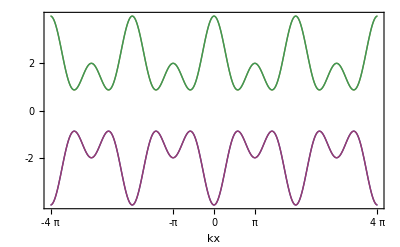

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1t2.png

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky]
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
ξ=α*Sqrt[Sin[kx]^2+Sin[ky]^2+mz^2];t=0.5;
α=0.0;mz=0.0;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
Image4=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-2,0,2},None},{{-Pi,-4 Pi,0,Pi,4 Pi},None}}]
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1t2.png",Image4]
```

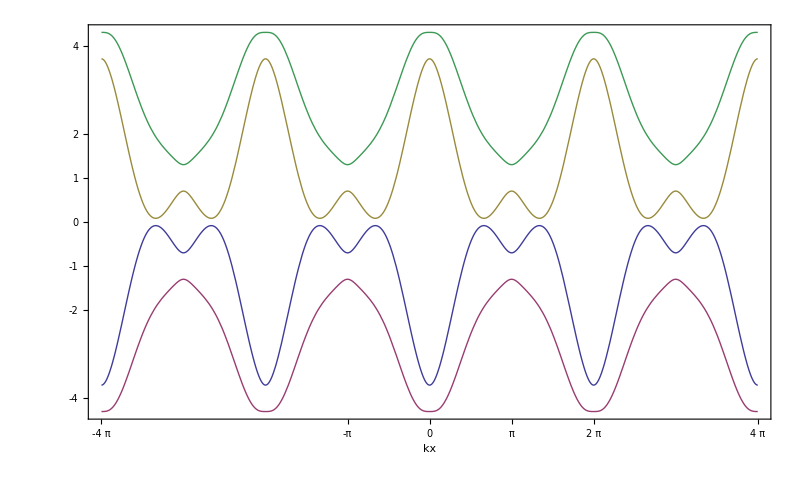

/home/nivedita/Documents/NiveditaNotes/Recent/new/omega40/edgestates_bulkproperties/Dispersiont1t2+alpha.png

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky];
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
ξ=Sqrt[α^2*Sin[kx]^2+Sin[ky]^2+mz^2];t=0.25;
α=1.0;mz=0.30;ky=0.0;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
Image5=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-4,-2,-1,0,1,2,4},None},{{-4Pi,2*Pi,-Pi,0,Pi,28Pi,4 Pi},None}}]
Export["/home/nivedita/Documents/NiveditaNotes/Recent/new/omega40/edgestates_bulkproperties/Dispersiont1t2+alpha.png",Image5]
```

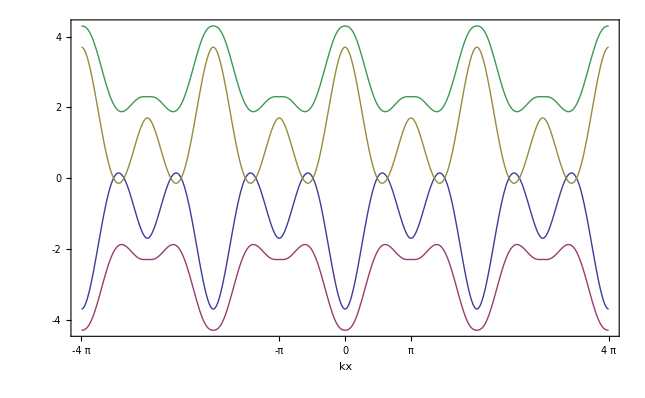

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky,mz]
ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
ξ=Sqrt[α^2*Sin[kx]^2+Sin[ky]^2+mz^2];t=0.50;
α=1.0;mz=0.30;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;ky=0.0;
Image6=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-4,-2,0,2,4},None},{{-4Pi,-Pi,0,Pi,4 Pi},None}}]
(*Image6=Plot[{En1[kx,ky],En2[kx,ky]},{kx,-4*Pi,4*Pi},AxesLabel->Automatic]*)
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1t2+alpha+mz.png",Image6];
```

```mathematica
Clear[ϵn,t,α,ξ,En1,En2,kx,ky,mz];

ϵn[kx_,ky_]:=-2*(1-t)*(Cos[kx]+Cos[ky])-2*t*(Cos[2*kx]+Cos[2*ky]);
α=4.0;mz=0.10;
ξ=Sqrt[α^2*(Sin[kx]^2+Sin[ky]^2)+mz^2];t=0.40;
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
```

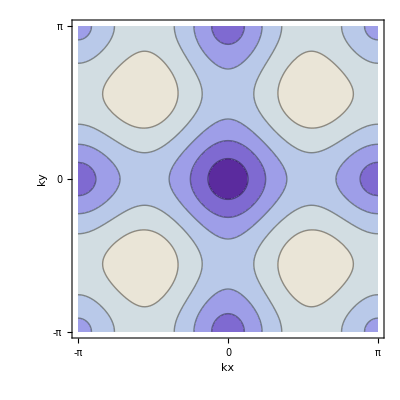

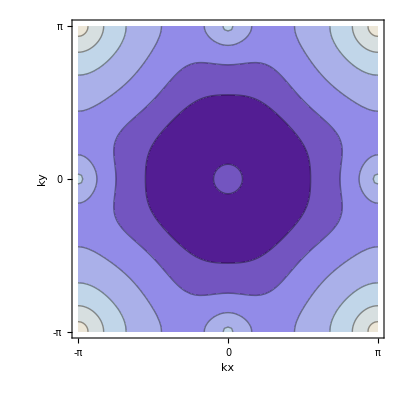

```mathematica
Image7=ContourPlot[En1[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]

Image8=ContourPlot[En2[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},Frame->True,FrameTicks-> {{-Pi,0,Pi},{-Pi,0,Pi}},FrameLabel-> {"kx","ky"},LabelStyle-> {Black,Large}]
```

```mathematica
Clear[ky];
```

```mathematica
ky=0;
```

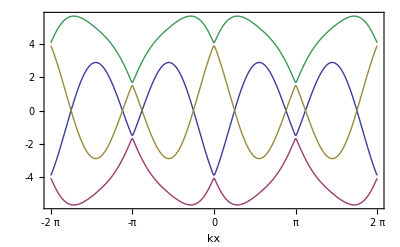

```mathematica
Image9=Plot[{En1[kx,ky],En2[kx,ky],-En1[kx,ky],-En2[kx,ky]},{kx,-2*Pi,2*Pi},AxesLabel->Automatic,Frame->True,FrameTicks->{{{-4,-2,0,2,4},None},{{-2*Pi,-Pi,0,Pi,2 Pi},None}}]
```